```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1;
```

### List of constants

```mathematica
EH=9.4;(*Hartree in eV*)
aB=9.97;(*Bohr radius in A*)
Eshift=10;(*energy shift*)
numE=1;(*number of eigenenergies to be solved for*)
r0=5; (*scale radius*)
γ=0.0513;(*effective mass ratio*)
maxcell=10^-4; (*maximum volume of the finite elements (relative to the volume of the total domain)*)
αmax=π/2.1;
pres=3;
Uc=0.215;
rc=0.1;
```

### Schrodinger equation and boundary conditions

```mathematica
U[r_]=Uc/(4π rc^3/3)HeavisideTheta[rc-r];
```

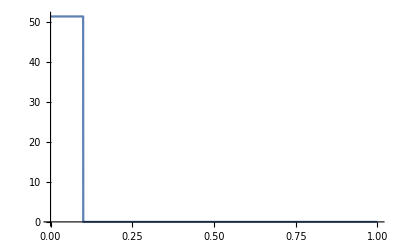

```mathematica
Plot[U[r],{r,0,1},Exclusions->None]
```

```mathematica
PDE0=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDEc=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-U[r]+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDE1=-(1/2)D[f1[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f1[r,θ],θ]- 1/(2 r^2)D[f1[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))- U[r]/4 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f1[r,θ]-3 U[r]/4 KroneckerDelta[m,0]f2[r,θ];
PDE2=-(1/2)D[f2[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f2[r,θ],θ]- 1/(2 r^2)D[f2[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-3 U[r]/4 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f2[r,θ]-U[r]/4 KroneckerDelta[m,0]f1[r,θ];
```

```mathematica
PDEctn=Simplify[PDEc/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;(* transform to tangent space r = r0 tan[αr] to map [0, ∞] in r to [0, π/2] in αr*)
PDE0tn=Simplify[PDE0/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
PDE1tn=Simplify[PDE1/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ; 
PDE2tn=Simplify[PDE2/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
```

```mathematica
Ω=ImplicitRegion[True,{{αr,0,αmax},{θ,0,Pi/2}}];
```

```mathematica
Γs=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γa=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ1s=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ1a=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ2s=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ2a=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; (*boundary condition for odd functions in θ'=π/2-θ*)
```

m=0 even parity states

```mathematica
{E0e,f0e}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0e=E0e-Eshift
```

{-1.36936}

m=0 odd parity states

```mathematica
{E0o,f0o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0},Γa},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0o=E0o-Eshift
```

{-0.508149}

```mathematica
(E0o[[1]]-E0e[[1]])/3
```

0.287071

m=1 odd parity states

```mathematica
{E1o,f1o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->1,Wn-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E1o=E1o-Eshift
```

{-0.183925}

```mathematica
(E1o[[1]]-E0e[[1]])/3
```

0.395146

### Normalization

```mathematica
N0e=ConstantArray[0,numE];
```

```mathematica
For[k=1,k<numE+1,k++,
N0e[[k]]=NIntegrate[(f0e[[k]])^2 r0 (Sec[αr])^2 Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->6,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ω=0.1; (*light frequency*)
```

```mathematica
W[x_]=x+E0e[[1]];
```

```mathematica
chi3[ω_]:=Module[{sols1101,g1101,sols1102,g1102,sols1112,g1112,sols4101,g4101,sols4102,g4102,sols4112,g4112,sols120,g1201,g1202,sols1212,g1212,sols1222,g1222,sols320,g3201,g3202,sols3212,g3212,sols3222,g3222,sols420,g4201,g4202,sols4212,g4212,sols4222,g4222,sols1301,g1301,sols1302,g1302,sols1312,g1312,sols2301,g2301,sols2302,g2302,sols2312,g2312,sols3301,g3301,sols3302,g3302,sols3312,g3312,sols4301,g4301,sols4302,g4302,sols4312,g4312,χ1,χ2,χ3,χ4,χ},
sols1101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1101[αr_,θ_]=sols1101[[1,1,2]][αr,θ];
sols1102=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/3/.{m->0,Wn-> W[ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1102[αr_,θ_]=sols1102[[1,1,2]][αr,θ];
sols1112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]](√2/3)/.{m->1,Wn->  W[ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1112[αr_,θ_]=sols1112[[1,1,2]][αr,θ];
sols4101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[-3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4101[αr_,θ_]=sols4101[[1,1,2]][αr,θ];
sols4102=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/3/.{m->0,Wn-> W[-3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4102[αr_,θ_]=sols4102[[1,1,2]][αr,θ];
sols4112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]](√2/3)/.{m->1,Wn->  W[-3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4112[αr_,θ_]=sols4112[[1,1,2]][αr,θ];
sols120=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[2ω]},PDE2tn==√γ r0 Tan[αr]Cos[θ]g1102[αr,θ]/3+r0 Tan[αr]Sin[θ]g1112[αr,θ](2√2/3)/.{m->0,Wn->  W[2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1201[αr_,θ_]=sols120[[1,1,2]][αr,θ];
g1202[αr_,θ_]=sols120[[1,2,2]][αr,θ];
sols1212=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1112[αr,θ]/3+r0 Tan[αr]Sin[θ]g1102[αr,θ](√2/3)/.{m->1,Wn->  W[2ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1212[αr_,θ_]=sols1212[[1,1,2]][αr,θ];
sols1222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ](√2/3)/.{m->2,Wn->  W[2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1222[αr_,θ_]=sols1222[[1,1,2]][αr,θ];
sols320=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==√γ r0 Tan[αr]Cos[θ]g1102[αr,θ]/3+r0 Tan[αr]Sin[θ]g1112[αr,θ](2√2/3)/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3201[αr_,θ_]=sols320[[1,1,2]][αr,θ];
g3202[αr_,θ_]=sols320[[1,2,2]][αr,θ];
sols3212=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1112[αr,θ]/3+r0 Tan[αr]Sin[θ]g1102[αr,θ](√2/3)/.{m->1,Wn->  W[-2ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3212[αr_,θ_]=sols3212[[1,1,2]][αr,θ];
sols3222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ](√2/3)/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3222[αr_,θ_]=sols3222[[1,1,2]][αr,θ];
sols420=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g4101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==√γ r0 Tan[αr]Cos[θ]g4102[αr,θ]/3+r0 Tan[αr]Sin[θ]g4112[αr,θ](2√2/3)/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4201[αr_,θ_]=sols420[[1,1,2]][αr,θ];
g4202[αr_,θ_]=sols420[[1,2,2]][αr,θ];
sols4212=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g4112[αr,θ]/3+r0 Tan[αr]Sin[θ]g4102[αr,θ](√2/3)/.{m->1,Wn->  W[-2ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4212[αr_,θ_]=sols4212[[1,1,2]][αr,θ];
sols4222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g4112[αr,θ](√2/3)/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4222[αr_,θ_]=sols4222[[1,1,2]][αr,θ];
sols1301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1301[αr_,θ_]=sols1301[[1,1,2]][αr,θ];
sols1302=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1202[αr,θ]/3+r0 Tan[αr]Sin[θ]g1212[αr,θ](2√2/3)/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1302[αr_,θ_]=sols1302[[1,1,2]][αr,θ];
sols1312=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1212[αr,θ]/3+r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])(√2/3)/.{m->1,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1312[αr_,θ_]=sols1312[[1,1,2]][αr,θ];
sols2301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g2301[αr_,θ_]=sols2301[[1,1,2]][αr,θ];
sols2302=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1202[αr,θ]/3+r0 Tan[αr]Sin[θ]g1212[αr,θ](2√2/3)/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g2302[αr_,θ_]=sols2302[[1,1,2]][αr,θ];
sols2312=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g1212[αr,θ]/3+r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])(√2/3)/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g2312[αr_,θ_]=sols2312[[1,1,2]][αr,θ];
sols3301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g3201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3301[αr_,θ_]=sols3301[[1,1,2]][αr,θ];
sols3302=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g3202[αr,θ]/3+r0 Tan[αr]Sin[θ]g3212[αr,θ](2√2/3)/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3302[αr_,θ_]=sols3302[[1,1,2]][αr,θ];
sols3312=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g3212[αr,θ]/3+r0 Tan[αr]Sin[θ] (g3202[αr,θ]+g3222[αr,θ])(√2/3)/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3312[αr_,θ_]=sols3312[[1,1,2]][αr,θ];
sols4301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g4201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4301[αr_,θ_]=sols4301[[1,1,2]][αr,θ];
sols4302=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g4202[αr,θ]/3+r0 Tan[αr]Sin[θ]g4212[αr,θ](2√2/3)/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4302[αr_,θ_]=sols4302[[1,1,2]][αr,θ];
sols4312=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ]g4212[αr,θ]/3+r0 Tan[αr]Sin[θ] (g4202[αr,θ]+g4222[αr,θ])(√2/3)/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4312[αr_,θ_]=sols4312[[1,1,2]][αr,θ];
χ1=1/4 1/N0e[[1]] NIntegrate[f0e[[1]]g1301[αr,θ] √γ r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 3/4 1/N0e[[1]] NIntegrate[f0e[[1]]((2√2/3)g1312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ]+(√γ/3)g1302[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ]),{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ2=1/4 1/N0e[[1]] NIntegrate[f0e[[1]]g2301[αr,θ] √γ r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 3/4 1/N0e[[1]] NIntegrate[f0e[[1]]((2√2/3)g2312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ]+(√γ/3)g2302[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ]),{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ3=1/4 1/N0e[[1]] NIntegrate[f0e[[1]]g3301[αr,θ] √γ r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 3/4 1/N0e[[1]] NIntegrate[f0e[[1]]((2√2/3)g3312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ]+(√γ/3)g3302[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ]),{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ4=1/4 1/N0e[[1]] NIntegrate[f0e[[1]]g4301[αr,θ] √γ r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 3/4 1/N0e[[1]] NIntegrate[f0e[[1]]((2√2/3)g4312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ]+(√γ/3)g4302[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ]),{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ=χ1+χ2+χ3+χ4;
Return[{χ1,χ2,χ3,χ4,χ}];]
```

```mathematica
chi3[0.001]
```

{-6.1035,-6.08636,6.2873,6.26954,0.366982}

### Chi3 spectrum

```mathematica
ωmin=0;
ωmax=-0.99E0e[[1]]/3;
```

```mathematica
Nω=500;
```

```mathematica
ωL=Range[ωmin,ωmax,(ωmax-ωmin)/Nω];
χ3L=ConstantArray[0,{Length[ωL],5}];
```

```mathematica
SetSharedVariable[{χ3L,ωL,f0e}];
```

```mathematica
ParallelDo[
Print["ω_",k];
χ3L[[k,;;]]=chi3[ωL[[k]]]
,{k,1,Length[ωL]}]
```

ω_1

ω_9

ω_17

ω_25

ω_33

ω_41

ω_49

ω_57

ω_65

ω_73

ω_81

ω_89

ω_97

ω_105

ω_113

ω_121

ω_90

ω_98

ω_50

ω_82

ω_114

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω_18

ω_26

ω_2

ω_10

ω_34

ω_58

ω_66

ω_106

ω_74

ω_42

ω_122

ω_91

ω_99

ω_51

ω_83

ω_19

ω_35

ω_115

ω_59

ω_75

ω_11

ω_3

ω_67

ω_27

ω_43

ω_123

ω_107

ω_92

ω_52

ω_100

ω_84

ω_20

ω_36

ω_12

ω_116

ω_76

ω_124

ω_4

ω_44

ω_60

ω_68

ω_108

ω_28

ω_53

ω_101

ω_13

ω_85

ω_37

ω_93

ω_21

ω_125

ω_117

ω_77

ω_5

ω_45

ω_69

ω_109

ω_61

ω_29

ω_54

ω_102

ω_14

ω_86

ω_22

ω_94

ω_38

ω_46

ω_126

ω_118

ω_6

ω_62

ω_70

ω_110

ω_78

ω_30

ω_15

ω_103

ω_55

ω_87

ω_47

ω_95

ω_23

ω_39

ω_127

ω_63

ω_119

ω_71

ω_7

ω_111

ω_31

ω_79

ω_56

ω_16

ω_96

ω_104

ω_88

ω_24

ω_48

ω_40

ω_64

ω_128

ω_32

ω_120

ω_72

ω_8

ω_112

ω_80

ω_129

ω_137

ω_145

ω_153

ω_161

ω_169

ω_177

ω_185

ω_193

ω_201

ω_209

ω_217

ω_225

ω_233

ω_241

ω_249

ω_154

ω_162

ω_130

ω_138

ω_170

ω_146

ω_178

ω_194

ω_186

ω_202

ω_210

ω_234

ω_218

ω_242

ω_226

ω_250

ω_155

ω_163

ω_139

ω_171

ω_131

ω_179

ω_187

ω_195

ω_147

ω_203

ω_211

ω_235

ω_219

ω_227

ω_243

ω_251

ω_164

ω_156

ω_140

ω_132

ω_172

ω_188

ω_180

ω_148

ω_196

ω_204

ω_212

ω_236

ω_220

ω_244

ω_252

ω_228

ω_157

ω_165

ω_141

ω_189

ω_133

ω_173

ω_181

ω_197

ω_149

ω_205

ω_213

ω_237

ω_221

ω_245

ω_253

ω_229

ω_158

ω_166

ω_142

ω_190

ω_174

ω_134

ω_150

ω_206

ω_182

ω_198

ω_238

ω_214

ω_222

ω_246

ω_254

ω_230

ω_167

ω_143

ω_159

ω_191

ω_175

ω_183

ω_135

ω_207

ω_199

ω_151

ω_239

ω_247

ω_223

ω_255

ω_215

ω_231

ω_144

ω_168

ω_160

ω_192

ω_176

ω_136

ω_184

ω_208

ω_200

ω_152

ω_240

ω_256

ω_224

ω_216

ω_248

ω_232

ω_257

ω_265

ω_273

ω_281

ω_289

ω_297

ω_305

ω_313

ω_321

ω_329

ω_337

ω_345

ω_353

ω_361

ω_369

ω_377

ω_282

ω_258

ω_274

ω_266

ω_290

ω_298

ω_306

ω_314

ω_330

ω_322

ω_338

ω_346

ω_354

ω_362

ω_370

ω_378

ω_259

ω_275

ω_283

ω_267

ω_291

ω_315

ω_307

ω_299

ω_331

ω_323

ω_339

ω_347

ω_363

ω_355

ω_371

ω_379

ω_276

ω_284

ω_260

ω_268

ω_292

ω_316

ω_308

ω_300

ω_332

ω_324

ω_340

ω_348

ω_364

ω_356

ω_372

ω_380

ω_285

ω_277

ω_261

ω_269

ω_293

ω_309

ω_317

ω_301

ω_325

ω_333

ω_341

ω_349

ω_365

ω_373

ω_357

ω_381

ω_286

ω_278

ω_262

ω_270

ω_294

ω_310

ω_302

ω_318

ω_334

ω_326

ω_342

ω_350

ω_366

ω_374

ω_358

ω_382

ω_287

ω_279

ω_263

ω_271

ω_295

ω_303

ω_311

ω_319

ω_327

ω_343

ω_335

ω_351

ω_375

ω_367

ω_359

ω_383

ω_288

ω_280

ω_264

ω_272

ω_296

ω_304

ω_320

ω_312

ω_328

ω_344

ω_336

ω_376

ω_368

ω_352

ω_360

ω_384

ω_385

ω_393

ω_401

ω_409

ω_417

ω_425

ω_432

ω_439

ω_446

ω_453

ω_460

ω_467

ω_474

ω_481

ω_488

ω_495

ω_386

ω_402

ω_394

ω_410

ω_418

ω_426

ω_433

ω_440

ω_461

ω_454

ω_447

ω_468

ω_475

ω_482

ω_489

ω_496

ω_387

ω_403

ω_395

ω_419

ω_411

ω_427

ω_434

ω_441

ω_462

ω_455

ω_448

ω_469

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

ω_483

ω_476

ω_490

ω_497

ω_388

ω_396

ω_404

ω_412

ω_420

ω_428

ω_435

ω_456

ω_442

ω_463

ω_449

ω_470

ω_477

ω_484

ω_491

ω_498

ω_389

ω_397

ω_405

ω_421

ω_413

ω_429

ω_436

ω_443

ω_457

ω_450

ω_464

ω_471

ω_492

ω_478

ω_485

ω_499

ω_390

ω_398

ω_406

ω_422

ω_414

ω_430

ω_437

ω_444

ω_458

ω_451

ω_465

ω_472

ω_493

ω_479

ω_486

ω_500

ω_391

ω_407

ω_399

ω_423

ω_415

ω_438

ω_431

ω_452

ω_445

ω_459

ω_466

ω_473

ω_494

ω_480

ω_487

ω_501

ω_392

ω_408

ω_400

ω_424

ω_416

```mathematica
DumpSave["chi3_GeP_MV_pr.mx",{ωL,χ3L}];
```